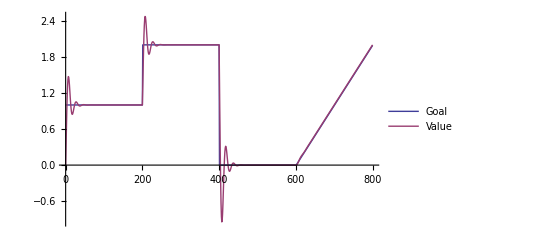

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.txt","Data"];
goaldata=Transpose[{Transpose[data][[1]],Transpose[data][[2]]}];
valuedata=Transpose[{Transpose[data][[1]],Transpose[data][[3]]}];
ListLinePlot[{goaldata,valuedata},PlotLegends->{"Goal","Value"}]
(*Export["image.pdf",%];*)
```